# Power spectrum of an audio wav file

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"];
```

## Get current notebook directory

```mathematica
CurrentNotebookDirectory=NotebookDirectory[SelectedNotebook[]]
```

/Users/Soha/Google Drive/Café Planck/1-Mathematics/Fourier analysis/07-FFT/

## Set Directory to current notebook directory

```mathematica
SetDirectory[CurrentNotebookDirectory]
```

/Users/Soha/Google Drive/Café Planck/1-Mathematics/Fourier analysis/07-FFT

## Listing contents of directories

```mathematica
FileNames["*.wav"]
```

{Signal-1.wav,Signal-2.wav,Signal and Noise.wav}

## Choose an audio file name

```mathematica
fname="Signal-2.wav";
```

## Elements of audio file

### Sound

```mathematica
Import[fname,"Sound"]
```

-Graphics-

### Audio Channels

```mathematica
audioChannels=Import[fname,"AudioChannels"]
```

1

### Audio Encoding

```mathematica
audioEncoding=Import[fname,"AudioEncoding"]
```

Integer16

### Sample Rate

```mathematica
sampleRate=Import[fname,"SampleRate"]
```

8000

### samples

```mathematica
samples=Import[fname,"Data"];
```

### samples Range

```mathematica
samplesRange={Min[samples],Max[samples]}
```

{-0.999878,0.999878}

### Number of samples

```mathematica
nSamples=Length[samples[[1]]]
```

24000

### Time

```mathematica
Time=nSamples/sampleRate//N
```

3.

## List Plot

```mathematica
t=0.01;
```

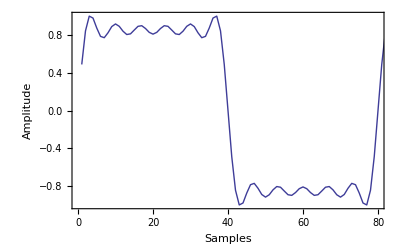

```mathematica
ListPlot[samples,Joined->True,Frame->True,FrameLabel->{"Samples","Amplitude"},PlotRange->{{0,t sampleRate},samplesRange}]
```

## Discrete Fourier transform

Ref

```mathematica
F=Fourier[samples[[1]],FourierParameters->{1,-1}];
```

```mathematica
nUniquePts=Ceiling[(nSamples+1)/2];
```

```mathematica
F=F[[1;;nUniquePts]];
```

```mathematica
F=Abs[F];
```

```mathematica
F=F/nSamples;
```

```mathematica
F=F^2;
```

```mathematica
If[OddQ[nSamples],F[[2;;-1]]=2F[[2;;-1]],F[[2;;-2]]=2F[[2;;-2]]];
```

```mathematica
fr=(Range[0,nUniquePts-1] sampleRate)/nSamples;
```

## Piks

```mathematica
nPiks=6;
```

```mathematica
piks=Table[{Pick[fr,F,RankedMax[F,i]][[1]],RankedMax[F,i]},{i,1,nPiks}];
N[piks]//TableForm
```

100.  | 0.591408 
300.  | 0.0657132 
500.  | 0.0236571 
700.  | 0.0120697 
900.  | 0.00730121 
1100.  | 0.00488727

### Frequency (Hz)

```mathematica
f=piks[[All,1]]//N//Sort
```

{100.,300.,500.,700.,900.,1100.}

### Angular frequency (Rad/s)

```mathematica
ω=2 π piks[[All,1]]//N//Sort
```

{628.319,1884.96,3141.59,4398.23,5654.87,6911.5}

## Frequency spectrum of the audio signal

```mathematica
plotRange={{0,1200},{0,0.6}};
```

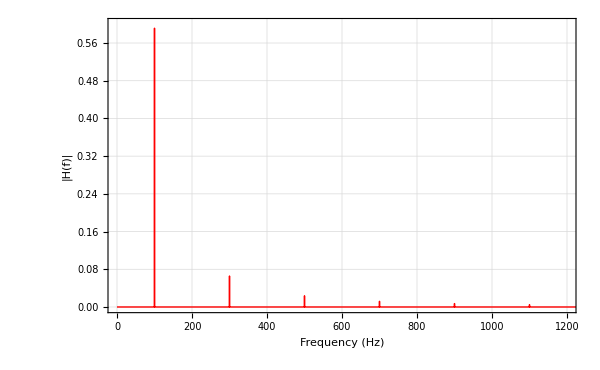

```mathematica
ListPlot[Transpose[{fr,F}],Joined->True,FrameLabel->{{"|H(f)|",None},{"Frequency (Hz)","Frequency spectrum of the audio signal"}},Frame-> True,PlotRange->plotRange,ImageSize->600,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->Red]
```

## Play audio signal

```mathematica
Play[∑_(i=1)^nPiks Sin[ω[[i]] t],{t,0,3}]
```

-Graphics-